# Report Project X

Course code: KTH/EECS:IX1501 - Mathematical Statistics
Date: 2019-09-09

Erik Lenas, eriklen@kth.se
Melker Mossberg, melkermo@kth.se

Task 1: “Winning a Teddy”

## Summery

### Task

At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up.

At a fun-fair you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

Determine the exact (no floating point, please) probability function of the sum.

Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

Determine the expected investment to win a Teddy.

What’s the probability of winning (at least one) Teddy if you play twenty times?

### Result

The probability density function
Let  p_x_1,p_x_2,p_x_3,p_x_4,p_x_5 be the probability functions of each dice. Then the PDF of  the dice’s convolution distribution ( p_S_n) can be defined as a recursive summation of  p_x_nmultiplied with  p_(S_(n-1)).

```mathematica
Subscript[p, Subscript[X, 1]](k)=1/4,k={1,2,3,4}
Subscript[p, Subscript[X, 2]](k)=1/6,k={1,2,... ,6}
Subscript[p, Subscript[X, 3]](k)=1/8,k={1,2,... ,8}
Subscript[p, Subscript[X, 4]](k)=1/12,k={1,2,... ,12}
Subscript[p, Subscript[X, 5]](k)=1/20,k={1,2,... ,20}
PDF=Piecewise[{{Subscript[p, Subscript[S, 1]](k) = ∑ _(i=0)^10 Subscript[p, Subscript[X, 2]](i)×Subscript[p, Subscript[X, 1]](k-i), k=(2,3,... , 10)}, {Subscript[p, Subscript[S, n]](k) = ∑ _i Subscript[p, Subscript[S, n-1]](i)×Subscript[p, Subscript[X, n]](k-i), k=(2,3,... , 50)}}]
```

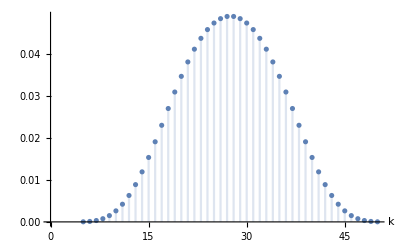

The exact probability of winning a teddy-bear P( X ≤ 10  ||  X≥ 50 ) 
Since the distribution is symmetrical around X = 55/2, we can multiply  the result of 
P( X ≤ 10) by 2 to get our answer. Probability of winning = p_w.

```mathematica
Subscript[p, W] = 2 × P(X≤10) =2  × ∑_(k=0)^10 PDF(k) =41/3840 ≈0.010677
```

The expected  investment to win a teddy-bear 
This can be calculated as the expected number of throws, multiplied with the cost of one throw. The expected number of throws is calculated by summing the probability of a n throws before a win, multiplied with n, from 0 to infinity.

```mathematica
( ∑_(i=1)^∞ (1-Subscript[p, W])^(i-1) ×  Subscript[p, W] × i) × 2 = 7680/41 ≈187.31707
```

The probability of winning at least once in 20 throws 
This can be calculated as the inverse probability of not winning in twenty throws.

```mathematica
1-(1-Subscript[p, W])^20 =
```

```mathematica
93896720713692929068924170210101909985514754789674511350420879336475999/485986815555701405566977235358756074107883642001817600000000000000000000
≈0.1932084
```

The expected value and standard deviation
The expected value (µ), variant(V) and standard deviation(σ) of a discrete convolution can be calculated as

```mathematica
µ = ∑_(k=-∞)^∞ PDF(k)×k = ∑_(k=5)^50 PDF(k)×k  = 55/2
V =  ∑_(k=5)^50 PDF(k)×(k-µ)^2 = 655/12
σ = √V=(√(655/3))/2
```

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
(* TASK 1: PDF of convolution of all platonic dice *)
```

```mathematica
Subscript[pfX, 4][k_]:=Piecewise[{{1/4,1≤k≤4}}];
Subscript[pfX, 6][k_]:=Piecewise[{{1/6,1≤k≤6}}]
Subscript[pfX, 8][k_]:=Piecewise[{{1/8,1≤k≤8}}];
Subscript[pfX, 12][k_]:=Piecewise[{{1/12,1≤k≤12}}];
Subscript[pfX, 20][k_]:=Piecewise[{{1/20,1≤k≤20}}];
```

```mathematica
pfS1[s_]:=pfS1[s]= Sum[Subscript[pfX, 4][n]*Subscript[pfX, 6][s-n],{n,0,10}];
pfS2[s_]:= pfS2[s]=Sum[pfS1[n]*Subscript[pfX, 8][s-n],{n,0,18}];
pfS3[s_]:= pfS3[s]=Sum[pfS2[n]*Subscript[pfX, 12][s-n],{n,0,30}];
pfS4[s_]:= pfS4[s]=Sum[pfS3[n]*Subscript[pfX, 20][s-n],{n,0,50}]
```

```mathematica
DiscretePlot[pfS4[k],{k,5,50}, AxesLabel->Automatic]
```

-Graphics-

```mathematica
(* TASK 2: Probability of winning *)
```

```mathematica
cWin = Sum[pfS4[x],{x,0,10}]*2    (* Symetrical distribution*)
```

41/3840

```mathematica
N[41/3840]
```

0.0106771

```mathematica
(* TASK 3: Expected num of throws, multiplied by price *)
```

```mathematica
ExpNumThrow = Sum[(1-cWin)^(n-1)*cWin*n,{n,1,Infinity}];
Cost = 2;
ExpCost = ExpNumThrow * Cost
```

7680/41

```mathematica
N[ExpCost]
```

187.317

```mathematica
(* TASK 4: Chance of winning at least once in 20 throws *)
```

```mathematica
1-(1-cWin)^20
```

93896720713692929068924170210101909985514754789674511350420879336475999/485986815555701405566977235358756074107883642001817600000000000000000000

```mathematica
N[1-(1-cWin)^20]
```

0.193208

```mathematica
(* TASK 5: Expected value and standard deviation *)
```

```mathematica
µ =Sum[pfS4[n]*n,{n,5,50}]
```

55/2

```mathematica
V=Sum[(n-µ)^2*pfS4[n],{n,5,50}]
```

655/12

```mathematica
σ = Sqrt[V]
```

(√(655/3))/2

```mathematica
(* TASK 6: Determine using built-in normal distribution *)
```

```mathematica
𝒟=NormalDistribution[µ,σ]
```

NormalDistribution[55/2,(√(655/3))/2]

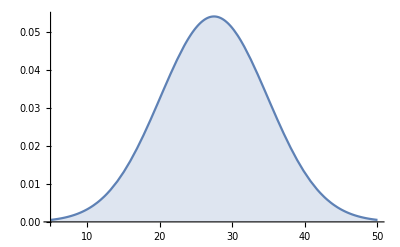

```mathematica
Plot[Table[PDF[𝒟,x],{μ,{1}}]//Evaluate,{x,5,50},Filling->Axis]
```